```mathematica
(*spherical pendulum 算例1*)
list=RungeK[{pθ,2^(-3/4)/Sin[θ]^2,1/(2 √2)Cos[θ]/Sin[θ]^3-Sin[θ]},{θ,ϕ,pθ},{π/4,0,0},{2π,0.01}]
```

```mathematica
(*初值取 OverDot[Subscript[ϕ, 0]]=√(g/(l Cos[Subscript[θ, 0]]))=2^(1/4),g/l 取1，Subscript[ϕ, 0]=0,Subscript[θ, 0]=π/4,Subscript[θ, 0]^。=0,而pθ=θ^。，由中学物理的知识可知此时重力与拉力的合力刚好提供向心力，此时摆球作匀速圆周运动，查看数值算例发现θ和pθ在2π的时间内基本不变说明了这一点，对于ϕ,转速为2^(1/4),2π的时间内角度变化为*)
```

```mathematica
(2^(1/4))*2π//N
```

7.47201

```mathematica
(*与数值算例的值7.468稳合较好*)
```

```mathematica
(*spherical pendulum 算例2*)
list=RungeK[{pθ,(x^2*y)/Sin[θ]^2,x^4*y^2*Cos[θ]/Sin[θ]^3-Sin[θ]}/.{x->√(7/12),y->(12/5)^(1/4)},{θ,ϕ,pθ},{ArcCos[√(5/12)],0,0.05},{4*π,0.01}]
```

```mathematica
(*初值取 Subscript[ϕ, 0]=0,Subscript[θ, 0]^。=0,g/l 取1，而pθ=θ̇,Subscript[考虑到θ, 0] Subscript[在θ, e] 附近，结合angular moment convervation
可推出 OverDot[Subscript[ϕ, 0]]=√(g/(l Cos[Subscript[θ, 0]])),结合ω的公式可知要使轨道闭合则必须有ω/OverDot[Subscript[ϕ, 0]]=√(Cos[Subscript[θ, 0]]/OverDot[Subscript[ϕ, 0]]^2+Sin[Subscript[θ, 0]]^2+3*Cos[Subscript[θ, 0]]^2)为有理数,
Subscript[为此可取θ, 0]=ArcCos[√(5/12)]，OverDot[Subscript[ϕ, 0]]=(12/5)^(1/4),ω/OverDot[Subscript[ϕ, 0]]=3/2,从而使得ϕ转两周而θ转三周，数值解法给出精确解的图形如下*)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

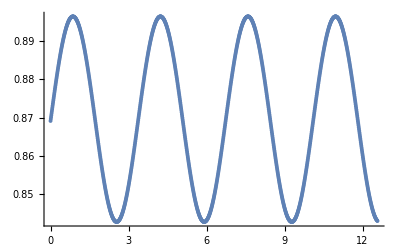

```mathematica
(*可以看出球摆轨道在转两圈之后闭合，进一步分析ϕ走过4π时用时为10.11,可求出相应的θ=0.869,查下图可知θ走过三个简谐振动周期*)
```

```mathematica
(*Subscript[θ, 0]^。会影响到总能量，事实上（1）的情形对应等效势V(θ)=-m g r Cos[θ]+L^2/(2*m*r^2*Sin[θ]^2)的最低点，而初值条件又恰好使得E=V(θ)故θ始终保持不变，而θ若有一很小的初速，则可对势能项在最低点作展开，即用一二次函数来近似V(θ)从而可求出θ作简谐振动的frequency为ω=√((g(1+3*Cos[Subscript[θ, e]]^2))/rCos[Subscript[θ, e]]),Subscript[θ, e] 为平衡位置的角度,若θ变化不大，由角动量守恒方程可近似认为 ϕ̇ 为常数，取ϕ̇/ω=rational number 即可得到闭合的轨道*)
```

```mathematica
(*以下内容作废*)
```

```mathematica
(*仅仅将 Subscript[θ, 0]^。初值由0改为0.1即可，数值算例给出θ随时间变化图如下,可以看出很像正弦曲线，与理论结果
θ=Subscript[θ, 0]+0.1/Ω Sin[Ωt],其中δθ适合微分方程-Graphics-*)
```

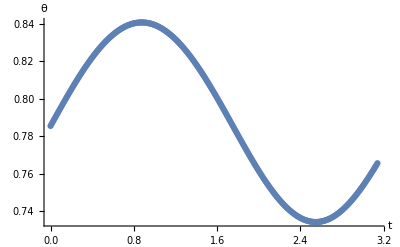

```mathematica
(*理论结果给出:*)
```

```mathematica
Ω=2^(1/4)*√(1+3/2)
```

```mathematica
(*θ变化的频率和初速无关*)
```

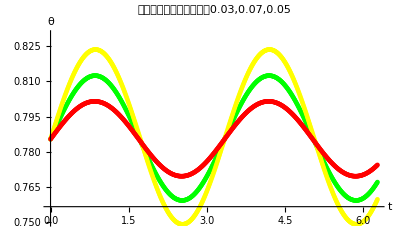

(√5)/2^(1/4)

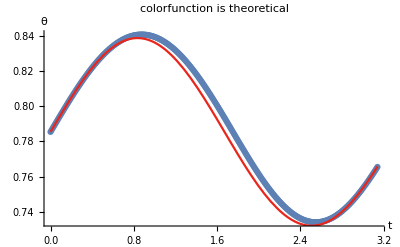

```mathematica
(*Reference:http://farside.ph.utexas.edu/teaching/336k/Newton/node82.html*)
```

```mathematica
(*由于θ的变化与 π/4 偏离不大，由角动量守恒方程可近似认为 ϕ̇ 不变，因此ϕ随时间近似线性变化,图像为过原点的直线，斜率为 OverDot[Subscript[ϕ, 0]]=2^(1/4)*)
```